```mathematica
pauliStringMultiplier[]:="I"
pauliStringMultiplier[s_String]:=s
pauliStringMultiplier[s1_String,s2_String]/;Length[StringCases[s1,"X"|"Y"|"Z"|"I"]]==Length[StringCases[s2,"X"|"Y"|"Z"|"I"]]:=
Module[{factor,multi},
factor=StringCases[s1<>s2,"ⅈ"|"-"];
multi=StringJoin[StringJoin@@@Transpose[{StringCases[s1,"X"|"Y"|"Z"|"I"],StringCases[s2,"X"|"Y"|"Z"|"I"]}]/.{x_String/;StringCount[x,"I"]==1:>StringDelete[x,"I"],"II"|"XX"|"YY"|"ZZ":>"I","XZ":>"-ⅈY","ZX":>"ⅈY","XY":>"ⅈZ","YX":>"-ⅈZ","YZ":>"ⅈX","ZY":>"-ⅈX"}];
factor=StringDelete["1"]@StringReplace[{"-1":>"-","I":>"ⅈ"}]@ToString[Times@@KeyValueMap[#1^#2&]@Counts[Join[factor,StringCases[multi,"ⅈ"|"-"]]/.{"-":>-1,"ⅈ"->ⅈ}]];
factor<>StringDelete[multi,{"-","ⅈ"}]]
pauliStringMultiplier[ss__String]:=Fold[pauliStringMultiplier,{ss}]
```

```mathematica
𝒢[n_]:=Catenate@Outer[#1<>#2&,{"","-","ⅈ","-ⅈ"},StringJoin@@@Tuples[{"I","X","Y","Z"},n]]
```

```mathematica
generators={"ⅈI","X","Y"};
elements=𝒢[1]
```

{I,X,Y,Z,-I,-X,-Y,-Z,ⅈI,ⅈX,ⅈY,ⅈZ,-ⅈI,-ⅈX,-ⅈY,-ⅈZ}

```mathematica
generators
```

```mathematica
table=Table[pauliStringMultiplier[i,j],{i,elements},{j,elements}];
table//TableForm[#,TableHeadings->{elements,elements}]&
```

| I | X | Y | Z | -I | -X | -Y | -Z | ⅈI | ⅈX | ⅈY | ⅈZ | -ⅈI | -ⅈX | -ⅈY | -ⅈZ
I | I | X | Y | Z | -I | -X | -Y | -Z | ⅈI | ⅈX | ⅈY | ⅈZ | -ⅈI | -ⅈX | -ⅈY | -ⅈZ
X | X | I | ⅈZ | -ⅈY | -X | -I | -ⅈZ | ⅈY | ⅈX | ⅈI | -Z | Y | -ⅈX | -ⅈI | Z | -Y
Y | Y | -ⅈZ | I | ⅈX | -Y | ⅈZ | -I | -ⅈX | ⅈY | Z | ⅈI | -X | -ⅈY | -Z | -ⅈI | X
Z | Z | ⅈY | -ⅈX | I | -Z | -ⅈY | ⅈX | -I | ⅈZ | -Y | X | ⅈI | -ⅈZ | Y | -X | -ⅈI
-I | -I | -X | -Y | -Z | I | X | Y | Z | -ⅈI | -ⅈX | -ⅈY | -ⅈZ | ⅈI | ⅈX | ⅈY | ⅈZ
-X | -X | -I | -ⅈZ | ⅈY | X | I | ⅈZ | -ⅈY | -ⅈX | -ⅈI | Z | -Y | ⅈX | ⅈI | -Z | Y
-Y | -Y | ⅈZ | -I | -ⅈX | Y | -ⅈZ | I | ⅈX | -ⅈY | -Z | -ⅈI | X | ⅈY | Z | ⅈI | -X
-Z | -Z | -ⅈY | ⅈX | -I | Z | ⅈY | -ⅈX | I | -ⅈZ | Y | -X | -ⅈI | ⅈZ | -Y | X | ⅈI
ⅈI | ⅈI | ⅈX | ⅈY | ⅈZ | -ⅈI | -ⅈX | -ⅈY | -ⅈZ | -I | -X | -Y | -Z | I | X | Y | Z
ⅈX | ⅈX | ⅈI | -Z | Y | -ⅈX | -ⅈI | Z | -Y | -X | -I | -ⅈZ | ⅈY | X | I | ⅈZ | -ⅈY
ⅈY | ⅈY | Z | ⅈI | -X | -ⅈY | -Z | -ⅈI | X | -Y | ⅈZ | -I | -ⅈX | Y | -ⅈZ | I | ⅈX
ⅈZ | ⅈZ | -Y | X | ⅈI | -ⅈZ | Y | -X | -ⅈI | -Z | -ⅈY | ⅈX | -I | Z | ⅈY | -ⅈX | I
-ⅈI | -ⅈI | -ⅈX | -ⅈY | -ⅈZ | ⅈI | ⅈX | ⅈY | ⅈZ | I | X | Y | Z | -I | -X | -Y | -Z
-ⅈX | -ⅈX | -ⅈI | Z | -Y | ⅈX | ⅈI | -Z | Y | X | I | ⅈZ | -ⅈY | -X | -I | -ⅈZ | ⅈY
-ⅈY | -ⅈY | -Z | -ⅈI | X | ⅈY | Z | ⅈI | -X | Y | -ⅈZ | I | ⅈX | -Y | ⅈZ | -I | -ⅈX
-ⅈZ | -ⅈZ | Y | -X | -ⅈI | ⅈZ | -Y | X | ⅈI | Z | ⅈY | -ⅈX | I | -Z | -ⅈY | ⅈX | -I

```mathematica
(* https://people.maths.bris.ac.uk/~matyd/GroupNames/1/C4oD4.htmlhttps://people.maths.bris.ac.uk/~matyd/GroupNames/1/C4oD4.htmlNonehttps://people.maths.bris.ac.uk/~matyd/GroupNames/1/C4oD4.htmlHyperlinkActionRecycledHyperlinkActive *)
group8=PermutationGroup[{Cycles[{{1,2,3,4},{5,6,7,8}}],Cycles[{{1,4,3,2},{5,6,7,8}}],Cycles[{{1,6},{2,7},{3,8},{4,5}}]}];
group16=PermutationGroup[{Cycles[{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}],Cycles[{{1,13,3,15},{2,14,4,16},{5,11,7,9},{6,12,8,10}}],Cycles[{{1,11},{2,12},{3,9},{4,10},{5,13},{6,14},{7,15},{8,16}}]}];
```

```mathematica
Ordering/@table
```

{{5,1,6,2,7,3,8,4,13,9,14,10,15,11,16,12},{6,2,5,1,16,12,11,15,14,10,13,9,4,8,7,3},{7,3,12,16,5,1,14,10,15,11,8,4,13,9,2,6},{8,4,15,11,10,14,5,1,16,12,3,7,6,2,13,9},{1,5,2,6,3,7,4,8,9,13,10,14,11,15,12,16},{2,6,1,5,12,16,15,11,10,14,9,13,8,4,3,7},{3,7,16,12,1,5,10,14,11,15,4,8,9,13,6,2},{4,8,11,15,14,10,1,5,12,16,7,3,2,6,9,13},{9,13,10,14,11,15,12,16,5,1,6,2,7,3,8,4},{10,14,9,13,8,4,3,7,6,2,5,1,16,12,11,15},{11,15,4,8,9,13,6,2,7,3,12,16,5,1,14,10},{12,16,7,3,2,6,9,13,8,4,15,11,10,14,5,1},{13,9,14,10,15,11,16,12,1,5,2,6,3,7,4,8},{14,10,13,9,4,8,7,3,2,6,1,5,12,16,15,11},{15,11,8,4,13,9,2,6,3,7,16,12,1,5,10,14},{16,12,3,7,6,2,13,9,4,8,11,15,14,10,1,5}}

```mathematica
perm=FindPermutation[
Position[#,1,{2},Heads->False][[All,2]]&@GroupMultiplicationTable[group16],
Position[#,1,{2},Heads->False][[All,2]]&@GroupMultiplicationTable[group8]
]
```

Cycles[{{2,7,4},{3,8,6},{10,12,13,15},{11,16}}]

```mathematica
#[[Position[#,1,{2},Heads->False][[All,2]]]]&@GroupMultiplicationTable[group8]//Diagonal
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(Transpose[Permute[Transpose[Permute[GroupMultiplicationTable[group16],perm]],perm]])==GroupMultiplicationTable[group8]
```

False

```mathematica
GroupMultiplicationTable@group16//Diagonal
```

{1,3,1,3,1,3,1,3,1,3,1,3,3,1,3,1}

```mathematica
Position[#,1,{2},Heads->False][[All,2]]&@GroupMultiplicationTable[group8]
```

{1,2,8,7,5,6,4,3,9,13,16,12,10,14,15,11}

```mathematica
iso=FindGraphIsomorphism[CayleyGraph[group16],CayleyGraph[group8]][[1]]
```

<|1→1,2→3,3→6,4→8,5→9,6→11,7→14,8→16,9→15,10→10,11→12,12→13,13→7,14→2,15→4,16→5|>

```mathematica
chooseIdentity // ClearAll
chooseIdentity[x_]:=With[{pos=Position[#,x,{2},Heads->False]},#[[pos[[All,2]],pos[[All,1]]]]]&;
```

```mathematica
GroupElementToWord[group16,#]&/@GroupElements[group16]
```

{{},{1},{-1,-1},{-1},{-3,-2},{1,-3,-2},{-2,-3},{1,-3,2},{1,-3,1},{-1,-3},{-3},{-3,1},{2},{-1,-2},{-2},{-1,2}}

```mathematica
elements=table[[1]]
inverses=elements[[Position[table,"I",{2},Heads->False][[All,2]]]]
```

{I,X,Y,Z,-I,-X,-Y,-Z,ⅈI,ⅈX,ⅈY,ⅈZ,-ⅈI,-ⅈX,-ⅈY,-ⅈZ}

{I,X,Y,Z,-I,-X,-Y,-Z,-ⅈI,-ⅈX,-ⅈY,-ⅈZ,ⅈI,ⅈX,ⅈY,ⅈZ}

```mathematica
hittingSets[sets:{___List}]:=Union@@@Tuples@MapThread[Replace[{Complement[##]},{{}}:>List/@#1]&,{#,UniqueElements[#]}]&@sets
```

```mathematica
Map[a|->Most@NestWhile[Append[#,pauliStringMultiplier[#[[-1]],a]]&,{a},DuplicateFreeQ],elements]
```

{{I},{X,I},{Y,I},{Z,I},{-I,I},{-X,I},{-Y,I},{-Z,I},{ⅈI,-I,-ⅈI,I},{ⅈX,-I,-ⅈX,I},{ⅈY,-I,-ⅈY,I},{ⅈZ,-I,-ⅈZ,I},{-ⅈI,-I,ⅈI,I},{-ⅈX,-I,ⅈX,I},{-ⅈY,-I,ⅈY,I},{-ⅈZ,-I,ⅈZ,I}}

```mathematica
Outer[{a,b}|->Most@NestWhile[Append[#,pauliStringMultiplier[#[[-1]],a]]&,{b},DuplicateFreeQ],elements,elements]
hittingSets/@%
```

{{{I},{X},{Y},{Z},{-I},{-X},{-Y},{-Z},{ⅈI},{ⅈX},{ⅈY},{ⅈZ},{-ⅈI},{-ⅈX},{-ⅈY},{-ⅈZ}},{{I,X},{X,I},{Y,-ⅈZ},{Z,ⅈY},{-I,-X},{-X,-I},{-Y,ⅈZ},{-Z,-ⅈY},{ⅈI,ⅈX},{ⅈX,ⅈI},{ⅈY,Z},{ⅈZ,-Y},{-ⅈI,-ⅈX},{-ⅈX,-ⅈI},{-ⅈY,-Z},{-ⅈZ,Y}},{{I,Y},{X,ⅈZ},{Y,I},{Z,-ⅈX},{-I,-Y},{-X,-ⅈZ},{-Y,-I},{-Z,ⅈX},{ⅈI,ⅈY},{ⅈX,-Z},{ⅈY,ⅈI},{ⅈZ,X},{-ⅈI,-ⅈY},{-ⅈX,Z},{-ⅈY,-ⅈI},{-ⅈZ,-X}},{{I,Z},{X,-ⅈY},{Y,ⅈX},{Z,I},{-I,-Z},{-X,ⅈY},{-Y,-ⅈX},{-Z,-I},{ⅈI,ⅈZ},{ⅈX,Y},{ⅈY,-X},{ⅈZ,ⅈI},{-ⅈI,-ⅈZ},{-ⅈX,-Y},{-ⅈY,X},{-ⅈZ,-ⅈI}},{{I,-I},{X,-X},{Y,-Y},{Z,-Z},{-I,I},{-X,X},{-Y,Y},{-Z,Z},{ⅈI,-ⅈI},{ⅈX,-ⅈX},{ⅈY,-ⅈY},{ⅈZ,-ⅈZ},{-ⅈI,ⅈI},{-ⅈX,ⅈX},{-ⅈY,ⅈY},{-ⅈZ,ⅈZ}},{{I,-X},{X,-I},{Y,ⅈZ},{Z,-ⅈY},{-I,X},{-X,I},{-Y,-ⅈZ},{-Z,ⅈY},{ⅈI,-ⅈX},{ⅈX,-ⅈI},{ⅈY,-Z},{ⅈZ,Y},{-ⅈI,ⅈX},{-ⅈX,ⅈI},{-ⅈY,Z},{-ⅈZ,-Y}},{{I,-Y},{X,-ⅈZ},{Y,-I},{Z,ⅈX},{-I,Y},{-X,ⅈZ},{-Y,I},{-Z,-ⅈX},{ⅈI,-ⅈY},{ⅈX,Z},{ⅈY,-ⅈI},{ⅈZ,-X},{-ⅈI,ⅈY},{-ⅈX,-Z},{-ⅈY,ⅈI},{-ⅈZ,X}},{{I,-Z},{X,ⅈY},{Y,-ⅈX},{Z,-I},{-I,Z},{-X,-ⅈY},{-Y,ⅈX},{-Z,I},{ⅈI,-ⅈZ},{ⅈX,-Y},{ⅈY,X},{ⅈZ,-ⅈI},{-ⅈI,ⅈZ},{-ⅈX,Y},{-ⅈY,-X},{-ⅈZ,ⅈI}},{{I,ⅈI,-I,-ⅈI},{X,ⅈX,-X,-ⅈX},{Y,ⅈY,-Y,-ⅈY},{Z,ⅈZ,-Z,-ⅈZ},{-I,-ⅈI,I,ⅈI},{-X,-ⅈX,X,ⅈX},{-Y,-ⅈY,Y,ⅈY},{-Z,-ⅈZ,Z,ⅈZ},{ⅈI,-I,-ⅈI,I},{ⅈX,-X,-ⅈX,X},{ⅈY,-Y,-ⅈY,Y},{ⅈZ,-Z,-ⅈZ,Z},{-ⅈI,I,ⅈI,-I},{-ⅈX,X,ⅈX,-X},{-ⅈY,Y,ⅈY,-Y},{-ⅈZ,Z,ⅈZ,-Z}},{{I,ⅈX,-I,-ⅈX},{X,ⅈI,-X,-ⅈI},{Y,Z,-Y,-Z},{Z,-Y,-Z,Y},{-I,-ⅈX,I,ⅈX},{-X,-ⅈI,X,ⅈI},{-Y,-Z,Y,Z},{-Z,Y,Z,-Y},{ⅈI,-X,-ⅈI,X},{ⅈX,-I,-ⅈX,I},{ⅈY,ⅈZ,-ⅈY,-ⅈZ},{ⅈZ,-ⅈY,-ⅈZ,ⅈY},{-ⅈI,X,ⅈI,-X},{-ⅈX,I,ⅈX,-I},{-ⅈY,-ⅈZ,ⅈY,ⅈZ},{-ⅈZ,ⅈY,ⅈZ,-ⅈY}},{{I,ⅈY,-I,-ⅈY},{X,-Z,-X,Z},{Y,ⅈI,-Y,-ⅈI},{Z,X,-Z,-X},{-I,-ⅈY,I,ⅈY},{-X,Z,X,-Z},{-Y,-ⅈI,Y,ⅈI},{-Z,-X,Z,X},{ⅈI,-Y,-ⅈI,Y},{ⅈX,-ⅈZ,-ⅈX,ⅈZ},{ⅈY,-I,-ⅈY,I},{ⅈZ,ⅈX,-ⅈZ,-ⅈX},{-ⅈI,Y,ⅈI,-Y},{-ⅈX,ⅈZ,ⅈX,-ⅈZ},{-ⅈY,I,ⅈY,-I},{-ⅈZ,-ⅈX,ⅈZ,ⅈX}},{{I,ⅈZ,-I,-ⅈZ},{X,Y,-X,-Y},{Y,-X,-Y,X},{Z,ⅈI,-Z,-ⅈI},{-I,-ⅈZ,I,ⅈZ},{-X,-Y,X,Y},{-Y,X,Y,-X},{-Z,-ⅈI,Z,ⅈI},{ⅈI,-Z,-ⅈI,Z},{ⅈX,ⅈY,-ⅈX,-ⅈY},{ⅈY,-ⅈX,-ⅈY,ⅈX},{ⅈZ,-I,-ⅈZ,I},{-ⅈI,Z,ⅈI,-Z},{-ⅈX,-ⅈY,ⅈX,ⅈY},{-ⅈY,ⅈX,ⅈY,-ⅈX},{-ⅈZ,I,ⅈZ,-I}},{{I,-ⅈI,-I,ⅈI},{X,-ⅈX,-X,ⅈX},{Y,-ⅈY,-Y,ⅈY},{Z,-ⅈZ,-Z,ⅈZ},{-I,ⅈI,I,-ⅈI},{-X,ⅈX,X,-ⅈX},{-Y,ⅈY,Y,-ⅈY},{-Z,ⅈZ,Z,-ⅈZ},{ⅈI,I,-ⅈI,-I},{ⅈX,X,-ⅈX,-X},{ⅈY,Y,-ⅈY,-Y},{ⅈZ,Z,-ⅈZ,-Z},{-ⅈI,-I,ⅈI,I},{-ⅈX,-X,ⅈX,X},{-ⅈY,-Y,ⅈY,Y},{-ⅈZ,-Z,ⅈZ,Z}},{{I,-ⅈX,-I,ⅈX},{X,-ⅈI,-X,ⅈI},{Y,-Z,-Y,Z},{Z,Y,-Z,-Y},{-I,ⅈX,I,-ⅈX},{-X,ⅈI,X,-ⅈI},{-Y,Z,Y,-Z},{-Z,-Y,Z,Y},{ⅈI,X,-ⅈI,-X},{ⅈX,I,-ⅈX,-I},{ⅈY,-ⅈZ,-ⅈY,ⅈZ},{ⅈZ,ⅈY,-ⅈZ,-ⅈY},{-ⅈI,-X,ⅈI,X},{-ⅈX,-I,ⅈX,I},{-ⅈY,ⅈZ,ⅈY,-ⅈZ},{-ⅈZ,-ⅈY,ⅈZ,ⅈY}},{{I,-ⅈY,-I,ⅈY},{X,Z,-X,-Z},{Y,-ⅈI,-Y,ⅈI},{Z,-X,-Z,X},{-I,ⅈY,I,-ⅈY},{-X,-Z,X,Z},{-Y,ⅈI,Y,-ⅈI},{-Z,X,Z,-X},{ⅈI,Y,-ⅈI,-Y},{ⅈX,ⅈZ,-ⅈX,-ⅈZ},{ⅈY,I,-ⅈY,-I},{ⅈZ,-ⅈX,-ⅈZ,ⅈX},{-ⅈI,-Y,ⅈI,Y},{-ⅈX,-ⅈZ,ⅈX,ⅈZ},{-ⅈY,-I,ⅈY,I},{-ⅈZ,ⅈX,ⅈZ,-ⅈX}},{{I,-ⅈZ,-I,ⅈZ},{X,-Y,-X,Y},{Y,X,-Y,-X},{Z,-ⅈI,-Z,ⅈI},{-I,ⅈZ,I,-ⅈZ},{-X,Y,X,-Y},{-Y,-X,Y,X},{-Z,ⅈI,Z,-ⅈI},{ⅈI,Z,-ⅈI,-Z},{ⅈX,-ⅈY,-ⅈX,ⅈY},{ⅈY,ⅈX,-ⅈY,-ⅈX},{ⅈZ,I,-ⅈZ,-I},{-ⅈI,-Z,ⅈI,Z},{-ⅈX,ⅈY,ⅈX,-ⅈY},{-ⅈY,-ⅈX,ⅈY,ⅈX},{-ⅈZ,-I,ⅈZ,I}}}

{{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}},{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}}}

```mathematica
hittingSets/@Tuples[hittingSets/@Outer[{a,b}|->Most@NestWhile[Append[#,pauliStringMultiplier[#[[-1]],b]]&,{a},DuplicateFreeQ],elements,elements]]
```

{{{-I,I,-X,X,-Y,Y,-Z,Z,-ⅈI,ⅈI,-ⅈX,ⅈX,-ⅈY,ⅈY,-ⅈZ,ⅈZ}}}

```mathematica
Thread[pauliStringMultiplier[elements,inverses]]
```

{I,I,I,I,I,I,I,I,I,I,I,I,I,I,I,I}

```mathematica
CayleyGraph[group16]
```

-Graphics-

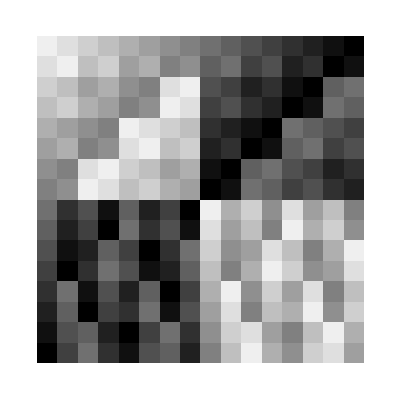

```mathematica
GroupMultiplicationTable[group8]//ArrayPlot
```

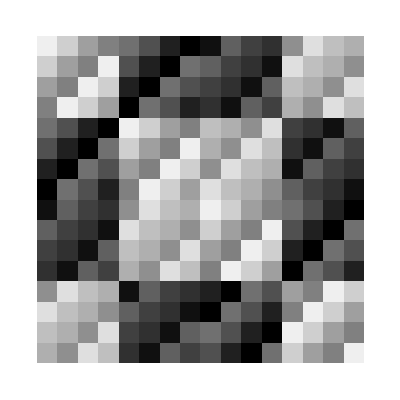

```mathematica
GroupMultiplicationTable[group16]/.iso//ArrayPlot
```

```mathematica
PermutationMatrix[perm].GroupMultiplicationTable[group16].PermutationMatrix[perm]ᵀ/.iso
```

{{1,8,11,14,9,16,3,6,15,4,5,10,13,2,7,12},{8,6,9,11,16,14,1,3,13,2,4,15,12,7,5,10},{11,9,6,8,3,1,14,16,5,10,12,7,4,15,13,2},{14,11,8,1,6,3,16,9,7,12,13,2,5,10,15,4},{9,16,3,6,1,8,11,14,4,15,10,5,2,13,12,7},{16,14,1,3,8,6,9,11,2,13,15,4,7,12,10,5},{3,1,14,16,11,9,6,8,10,5,7,12,15,4,2,13},{6,3,16,9,14,11,8,1,12,7,2,13,10,5,4,15},{15,13,2,4,7,5,10,12,1,14,16,3,8,11,9,6},{4,2,13,15,12,10,5,7,9,6,8,11,16,3,1,14},{5,4,15,10,13,12,7,2,11,8,1,14,9,6,3,16},{10,15,4,5,2,7,12,13,3,16,9,6,1,14,11,8},{13,12,7,2,5,4,15,10,8,11,14,1,6,9,16,3},{2,7,12,13,10,15,4,5,16,3,6,9,14,1,8,11},{7,5,10,12,15,13,2,4,14,1,3,16,11,8,6,9},{12,10,5,7,4,2,13,15,6,9,11,8,3,16,14,1}}

```mathematica
FindPermutation[Ordering/@table,Reverse@GroupMultiplicationTable[group16]]
```

FindPermutation::norel: Expressions {{5,1,6,2,7,3,8,4,13,9,«6»},{6,2,5,1,16,12,11,15,14,10,«6»},{7,3,12,16,5,1,14,10,15,11,«6»},{8,4,15,11,10,14,5,1,16,12,«6»},{1,5,2,6,3,7,4,8,9,13,«6»},{2,6,1,5,12,16,15,11,10,14,«6»},{3,7,16,12,1,5,10,14,11,15,«6»},{4,8,11,15,14,10,1,5,12,16,«6»},{9,13,10,14,11,15,12,16,5,1,«6»},{10,14,9,13,8,4,3,7,6,2,«6»},«6»} and {{16,13,14,15,12,9,10,11,6,7,«6»},{15,16,13,14,11,12,9,10,5,6,«6»},{14,15,16,13,10,11,12,9,8,5,«6»},{13,14,15,16,9,10,11,12,7,8,«6»},{12,9,10,11,16,13,14,15,4,1,«6»},{11,12,9,10,15,16,13,14,3,4,«6»},{10,11,12,9,14,15,16,13,2,3,«6»},{9,10,11,12,13,14,15,16,1,2,«6»},{8,5,6,7,4,1,2,3,14,15,«6»},{7,8,5,6,3,4,1,2,13,14,«6»},«6»} cannot be related by a permutation.

FindPermutation[{{5,1,6,2,7,3,8,4,13,9,14,10,15,11,16,12},{6,2,5,1,16,12,11,15,14,10,13,9,4,8,7,3},{7,3,12,16,5,1,14,10,15,11,8,4,13,9,2,6},{8,4,15,11,10,14,5,1,16,12,3,7,6,2,13,9},{1,5,2,6,3,7,4,8,9,13,10,14,11,15,12,16},{2,6,1,5,12,16,15,11,10,14,9,13,8,4,3,7},{3,7,16,12,1,5,10,14,11,15,4,8,9,13,6,2},{4,8,11,15,14,10,1,5,12,16,7,3,2,6,9,13},{9,13,10,14,11,15,12,16,5,1,6,2,7,3,8,4},{10,14,9,13,8,4,3,7,6,2,5,1,16,12,11,15},{11,15,4,8,9,13,6,2,7,3,12,16,5,1,14,10},{12,16,7,3,2,6,9,13,8,4,15,11,10,14,5,1},{13,9,14,10,15,11,16,12,1,5,2,6,3,7,4,8},{14,10,13,9,4,8,7,3,2,6,1,5,12,16,15,11},{15,11,8,4,13,9,2,6,3,7,16,12,1,5,10,14},{16,12,3,7,6,2,13,9,4,8,11,15,14,10,1,5}},{{16,13,14,15,12,9,10,11,6,7,8,5,2,3,4,1},{15,16,13,14,11,12,9,10,5,6,7,8,1,2,3,4},{14,15,16,13,10,11,12,9,8,5,6,7,4,1,2,3},{13,14,15,16,9,10,11,12,7,8,5,6,3,4,1,2},{12,9,10,11,16,13,14,15,4,1,2,3,8,5,6,7},{11,12,9,10,15,16,13,14,3,4,1,2,7,8,5,6},{10,11,12,9,14,15,16,13,2,3,4,1,6,7,8,5},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{8,5,6,7,4,1,2,3,14,15,16,13,10,11,12,9},{7,8,5,6,3,4,1,2,13,14,15,16,9,10,11,12},{6,7,8,5,2,3,4,1,16,13,14,15,12,9,10,11},{5,6,7,8,1,2,3,4,15,16,13,14,11,12,9,10},{4,1,2,3,8,5,6,7,12,9,10,11,16,13,14,15},{3,4,1,2,7,8,5,6,11,12,9,10,15,16,13,14},{2,3,4,1,6,7,8,5,10,11,12,9,14,15,16,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}}]

```mathematica
counts=ParallelTable[
gs->CountDistinct[With[{word=GroupElementToWord[group16,#]/.{i_Integer:>pauliStringMultiplier[If[Sign[i]==-1,"-I","I"],gs[[Abs[i]]]]}},
pauliStringMultiplier@@word
]&/@GroupElements[group16]],{gs,Tuples[elements,3]}];
```

```mathematica
Max@Association[counts]
```

16

```mathematica
GroupElementToWord[group16,#]&/@GroupElements[group16]
```

{{},{1},{-1,-1},{-1},{-3,-2},{1,-3,-2},{-2,-3},{1,-3,2},{1,-3,1},{-1,-3},{-3},{-3,1},{2},{-1,-2},{-2},{-1,2}}

```mathematica
GroupElementToWord[group8,#]&/@GroupElements[group8]
```

{{},{1,2},{1},{-2},{1,2,1,1},{1,1},{1,2,-1},{-1},{2,3},{1,2,2,3},{1,2,-3},{-3},{3,1},{1,2,3,1},{1,1,3},{1,2,1,1,3}}

```mathematica
With[{word=GroupElementToWord[group16,#]/.{i_Integer:>pauliStringMultiplier[If[Sign[i]==-1,"-I","I"],{"ⅈI","X","Z"}[[Abs[i]]]]}},
pauliStringMultiplier@@Echo@word
]&/@GroupElements[group16]
```

{}

{ⅈI}

{-ⅈI,-ⅈI}

{-ⅈI}

{-Z,-X}

{ⅈI,-Z,-X}

{-X,-Z}

{ⅈI,-Z,X}

{ⅈI,-Z,ⅈI}

{-ⅈI,-Z}

{-Z}

{-Z,ⅈI}

{X}

{-ⅈI,-X}

{-X}

{-ⅈI,X}

{I,ⅈI,-I,-ⅈI,ⅈY,-Y,-ⅈY,Y,Z,ⅈZ,-Z,-ⅈZ,X,ⅈX,-X,-ⅈX}

```mathematica
pauliStringMultiplier@@@Subsets[{"ⅈI","X","Z"},3]//CountDistinct
```

8

```mathematica
Keys@Select[Association[counts],EqualTo[16]]//Column
```

{ⅈI,X,Y}
{ⅈI,X,Z}
{ⅈI,X,-Y}
{ⅈI,X,-Z}
{ⅈI,X,ⅈY}
{ⅈI,X,ⅈZ}
{ⅈI,X,-ⅈY}
{ⅈI,X,-ⅈZ}
{ⅈI,Y,X}
{ⅈI,Y,Z}
{ⅈI,Y,-X}
{ⅈI,Y,-Z}
{ⅈI,Y,ⅈX}
{ⅈI,Y,ⅈZ}
{ⅈI,Y,-ⅈX}
{ⅈI,Y,-ⅈZ}
{ⅈI,Z,X}
{ⅈI,Z,Y}
{ⅈI,Z,-X}
{ⅈI,Z,-Y}
{ⅈI,Z,ⅈX}
{ⅈI,Z,ⅈY}
{ⅈI,Z,-ⅈX}
{ⅈI,Z,-ⅈY}
{ⅈI,-X,Y}
{ⅈI,-X,Z}
{ⅈI,-X,-Y}
{ⅈI,-X,-Z}
{ⅈI,-X,ⅈY}
{ⅈI,-X,ⅈZ}
{ⅈI,-X,-ⅈY}
{ⅈI,-X,-ⅈZ}
{ⅈI,-Y,X}
{ⅈI,-Y,Z}
{ⅈI,-Y,-X}
{ⅈI,-Y,-Z}
{ⅈI,-Y,ⅈX}
{ⅈI,-Y,ⅈZ}
{ⅈI,-Y,-ⅈX}
{ⅈI,-Y,-ⅈZ}
{ⅈI,-Z,X}
{ⅈI,-Z,Y}
{ⅈI,-Z,-X}
{ⅈI,-Z,-Y}
{ⅈI,-Z,ⅈX}
{ⅈI,-Z,ⅈY}
{ⅈI,-Z,-ⅈX}
{ⅈI,-Z,-ⅈY}
{ⅈI,ⅈX,Y}
{ⅈI,ⅈX,Z}
{ⅈI,ⅈX,-Y}
{ⅈI,ⅈX,-Z}
{ⅈI,ⅈX,ⅈY}
{ⅈI,ⅈX,ⅈZ}
{ⅈI,ⅈX,-ⅈY}
{ⅈI,ⅈX,-ⅈZ}
{ⅈI,ⅈY,X}
{ⅈI,ⅈY,Z}
{ⅈI,ⅈY,-X}
{ⅈI,ⅈY,-Z}
{ⅈI,ⅈY,ⅈX}
{ⅈI,ⅈY,ⅈZ}
{ⅈI,ⅈY,-ⅈX}
{ⅈI,ⅈY,-ⅈZ}
{ⅈI,ⅈZ,X}
{ⅈI,ⅈZ,Y}
{ⅈI,ⅈZ,-X}
{ⅈI,ⅈZ,-Y}
{ⅈI,ⅈZ,ⅈX}
{ⅈI,ⅈZ,ⅈY}
{ⅈI,ⅈZ,-ⅈX}
{ⅈI,ⅈZ,-ⅈY}
{ⅈI,-ⅈX,Y}
{ⅈI,-ⅈX,Z}
{ⅈI,-ⅈX,-Y}
{ⅈI,-ⅈX,-Z}
{ⅈI,-ⅈX,ⅈY}
{ⅈI,-ⅈX,ⅈZ}
{ⅈI,-ⅈX,-ⅈY}
{ⅈI,-ⅈX,-ⅈZ}
{ⅈI,-ⅈY,X}
{ⅈI,-ⅈY,Z}
{ⅈI,-ⅈY,-X}
{ⅈI,-ⅈY,-Z}
{ⅈI,-ⅈY,ⅈX}
{ⅈI,-ⅈY,ⅈZ}
{ⅈI,-ⅈY,-ⅈX}
{ⅈI,-ⅈY,-ⅈZ}
{ⅈI,-ⅈZ,X}
{ⅈI,-ⅈZ,Y}
{ⅈI,-ⅈZ,-X}
{ⅈI,-ⅈZ,-Y}
{ⅈI,-ⅈZ,ⅈX}
{ⅈI,-ⅈZ,ⅈY}
{ⅈI,-ⅈZ,-ⅈX}
{ⅈI,-ⅈZ,-ⅈY}
{ⅈX,Y,X}
{ⅈX,Y,-X}
{ⅈX,Z,X}
{ⅈX,Z,-X}
{ⅈX,-Y,X}
{ⅈX,-Y,-X}
{ⅈX,-Z,X}
{ⅈX,-Z,-X}
{ⅈX,ⅈY,X}
{ⅈX,ⅈY,-X}
{ⅈX,ⅈZ,X}
{ⅈX,ⅈZ,-X}
{ⅈX,-ⅈY,X}
{ⅈX,-ⅈY,-X}
{ⅈX,-ⅈZ,X}
{ⅈX,-ⅈZ,-X}
{ⅈY,X,Y}
{ⅈY,X,-Y}
{ⅈY,Z,Y}
{ⅈY,Z,-Y}
{ⅈY,-X,Y}
{ⅈY,-X,-Y}
{ⅈY,-Z,Y}
{ⅈY,-Z,-Y}
{ⅈY,ⅈX,Y}
{ⅈY,ⅈX,-Y}
{ⅈY,ⅈZ,Y}
{ⅈY,ⅈZ,-Y}
{ⅈY,-ⅈX,Y}
{ⅈY,-ⅈX,-Y}
{ⅈY,-ⅈZ,Y}
{ⅈY,-ⅈZ,-Y}
{ⅈZ,X,Z}
{ⅈZ,X,-Z}
{ⅈZ,Y,Z}
{ⅈZ,Y,-Z}
{ⅈZ,-X,Z}
{ⅈZ,-X,-Z}
{ⅈZ,-Y,Z}
{ⅈZ,-Y,-Z}
{ⅈZ,ⅈX,Z}
{ⅈZ,ⅈX,-Z}
{ⅈZ,ⅈY,Z}
{ⅈZ,ⅈY,-Z}
{ⅈZ,-ⅈX,Z}
{ⅈZ,-ⅈX,-Z}
{ⅈZ,-ⅈY,Z}
{ⅈZ,-ⅈY,-Z}
{-ⅈI,X,Y}
{-ⅈI,X,Z}
{-ⅈI,X,-Y}
{-ⅈI,X,-Z}
{-ⅈI,X,ⅈY}
{-ⅈI,X,ⅈZ}
{-ⅈI,X,-ⅈY}
{-ⅈI,X,-ⅈZ}
{-ⅈI,Y,X}
{-ⅈI,Y,Z}
{-ⅈI,Y,-X}
{-ⅈI,Y,-Z}
{-ⅈI,Y,ⅈX}
{-ⅈI,Y,ⅈZ}
{-ⅈI,Y,-ⅈX}
{-ⅈI,Y,-ⅈZ}
{-ⅈI,Z,X}
{-ⅈI,Z,Y}
{-ⅈI,Z,-X}
{-ⅈI,Z,-Y}
{-ⅈI,Z,ⅈX}
{-ⅈI,Z,ⅈY}
{-ⅈI,Z,-ⅈX}
{-ⅈI,Z,-ⅈY}
{-ⅈI,-X,Y}
{-ⅈI,-X,Z}
{-ⅈI,-X,-Y}
{-ⅈI,-X,-Z}
{-ⅈI,-X,ⅈY}
{-ⅈI,-X,ⅈZ}
{-ⅈI,-X,-ⅈY}
{-ⅈI,-X,-ⅈZ}
{-ⅈI,-Y,X}
{-ⅈI,-Y,Z}
{-ⅈI,-Y,-X}
{-ⅈI,-Y,-Z}
{-ⅈI,-Y,ⅈX}
{-ⅈI,-Y,ⅈZ}
{-ⅈI,-Y,-ⅈX}
{-ⅈI,-Y,-ⅈZ}
{-ⅈI,-Z,X}
{-ⅈI,-Z,Y}
{-ⅈI,-Z,-X}
{-ⅈI,-Z,-Y}
{-ⅈI,-Z,ⅈX}
{-ⅈI,-Z,ⅈY}
{-ⅈI,-Z,-ⅈX}
{-ⅈI,-Z,-ⅈY}
{-ⅈI,ⅈX,Y}
{-ⅈI,ⅈX,Z}
{-ⅈI,ⅈX,-Y}
{-ⅈI,ⅈX,-Z}
{-ⅈI,ⅈX,ⅈY}
{-ⅈI,ⅈX,ⅈZ}
{-ⅈI,ⅈX,-ⅈY}
{-ⅈI,ⅈX,-ⅈZ}
{-ⅈI,ⅈY,X}
{-ⅈI,ⅈY,Z}
{-ⅈI,ⅈY,-X}
{-ⅈI,ⅈY,-Z}
{-ⅈI,ⅈY,ⅈX}
{-ⅈI,ⅈY,ⅈZ}
{-ⅈI,ⅈY,-ⅈX}
{-ⅈI,ⅈY,-ⅈZ}
{-ⅈI,ⅈZ,X}
{-ⅈI,ⅈZ,Y}
{-ⅈI,ⅈZ,-X}
{-ⅈI,ⅈZ,-Y}
{-ⅈI,ⅈZ,ⅈX}
{-ⅈI,ⅈZ,ⅈY}
{-ⅈI,ⅈZ,-ⅈX}
{-ⅈI,ⅈZ,-ⅈY}
{-ⅈI,-ⅈX,Y}
{-ⅈI,-ⅈX,Z}
{-ⅈI,-ⅈX,-Y}
{-ⅈI,-ⅈX,-Z}
{-ⅈI,-ⅈX,ⅈY}
{-ⅈI,-ⅈX,ⅈZ}
{-ⅈI,-ⅈX,-ⅈY}
{-ⅈI,-ⅈX,-ⅈZ}
{-ⅈI,-ⅈY,X}
{-ⅈI,-ⅈY,Z}
{-ⅈI,-ⅈY,-X}
{-ⅈI,-ⅈY,-Z}
{-ⅈI,-ⅈY,ⅈX}
{-ⅈI,-ⅈY,ⅈZ}
{-ⅈI,-ⅈY,-ⅈX}
{-ⅈI,-ⅈY,-ⅈZ}
{-ⅈI,-ⅈZ,X}
{-ⅈI,-ⅈZ,Y}
{-ⅈI,-ⅈZ,-X}
{-ⅈI,-ⅈZ,-Y}
{-ⅈI,-ⅈZ,ⅈX}
{-ⅈI,-ⅈZ,ⅈY}
{-ⅈI,-ⅈZ,-ⅈX}
{-ⅈI,-ⅈZ,-ⅈY}
{-ⅈX,Y,X}
{-ⅈX,Y,-X}
{-ⅈX,Z,X}
{-ⅈX,Z,-X}
{-ⅈX,-Y,X}
{-ⅈX,-Y,-X}
{-ⅈX,-Z,X}
{-ⅈX,-Z,-X}
{-ⅈX,ⅈY,X}
{-ⅈX,ⅈY,-X}
{-ⅈX,ⅈZ,X}
{-ⅈX,ⅈZ,-X}
{-ⅈX,-ⅈY,X}
{-ⅈX,-ⅈY,-X}
{-ⅈX,-ⅈZ,X}
{-ⅈX,-ⅈZ,-X}
{-ⅈY,X,Y}
{-ⅈY,X,-Y}
{-ⅈY,Z,Y}
{-ⅈY,Z,-Y}
{-ⅈY,-X,Y}
{-ⅈY,-X,-Y}
{-ⅈY,-Z,Y}
{-ⅈY,-Z,-Y}
{-ⅈY,ⅈX,Y}
{-ⅈY,ⅈX,-Y}
{-ⅈY,ⅈZ,Y}
{-ⅈY,ⅈZ,-Y}
{-ⅈY,-ⅈX,Y}
{-ⅈY,-ⅈX,-Y}
{-ⅈY,-ⅈZ,Y}
{-ⅈY,-ⅈZ,-Y}
{-ⅈZ,X,Z}
{-ⅈZ,X,-Z}
{-ⅈZ,Y,Z}
{-ⅈZ,Y,-Z}
{-ⅈZ,-X,Z}
{-ⅈZ,-X,-Z}
{-ⅈZ,-Y,Z}
{-ⅈZ,-Y,-Z}
{-ⅈZ,ⅈX,Z}
{-ⅈZ,ⅈX,-Z}
{-ⅈZ,ⅈY,Z}
{-ⅈZ,ⅈY,-Z}
{-ⅈZ,-ⅈX,Z}
{-ⅈZ,-ⅈX,-Z}
{-ⅈZ,-ⅈY,Z}
{-ⅈZ,-ⅈY,-Z}

```mathematica
GroupMultiplicationTable@group//ArrayPlot
```

-Graphics-

### Outtakes

```mathematica
(* some weird group maker *)
GroupFromMultiplicationTable[
	table_ ? SquareMatrixQ,
	defaultIdentity_ : Automatic
] /; Equal @@ Sort /@ table :=
Enclose @ Block[{
	identity = Replace[defaultIdentity, Automatic -> table[[1, 1]]],
	n = Length[table],
	elements,
	cayleyTable
},
	cayleyTable = table[[Position[table, identity, {2}, Heads -> False][[All, 2]]]];
	PermutationGroup[
		PermutationCycles[SparseArray[Thread[Position[cayleyTable, #] -> 1]] . Range[n]] & /@ cayleyTable[[1]]
	]
]
```